```mathematica
Sum[b^(b/5)(1-b^(-1/3))(Factorial[b]/b^b),{b,1,40}]//N
```

0.717803

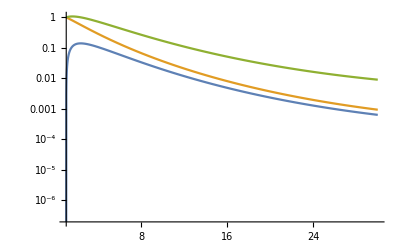

```mathematica
LogPlot[{b^(b/5)(1-b^(-1/3))(Factorial[b]/b^b),
b^(b/5)(Factorial[b]/b^b),
b^(b/5+2/3)(Factorial[b]/b^b)
},
{b,1,30}]
```

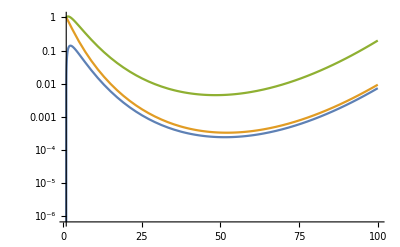

```mathematica
LogPlot[{b^(b/5)(1-b^(-1/3))(Factorial[b]/b^b),
b^(b/5)(Factorial[b]/b^b),
b^(b/5+2/3)(Factorial[b]/b^b)
},
{b,1,100}]
```

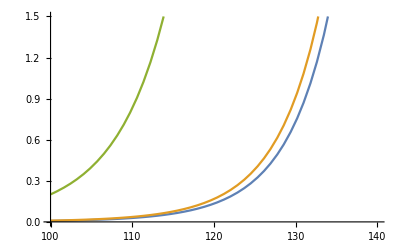

```mathematica
Plot[{b^(b/5)(1-b^(-1/3))(Factorial[b]/b^b),
b^(b/5)(Factorial[b]/b^b),
b^(b/5+2/3)(Factorial[b]/b^b)
},
{b,100,140},PlotRange->{0,1.5}]
```

```mathematica
NIntegrate[b^(b/5)*(1-b^(-1/3))(Factorial[b]/b^b),{b,1,30}]
```

0.739282

```mathematica
NIntegrate[b^(b/5)*(1-b^(-1/3))(Factorial[b]/b^b),{b,1,40}]
```

0.743651

```mathematica
NIntegrate[b^(b/5)*(1-b^(-1/3))(Factorial[b]/b^b),{b,60,80}]
```

0.00951244

```mathematica
nice[b_]:=b^(b/5)(1-b^(-1/3))(Factorial[b]/b^b)
```

```mathematica
nice[130.]
```

0.732964

```mathematica
nice[120.]
```

0.133535

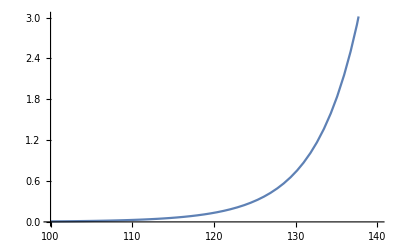

```mathematica
Plot[nice[b],{b,100,140}]
```

```mathematica
nicer[b_]:=Sum[nice[c],{c,60,b}]
```

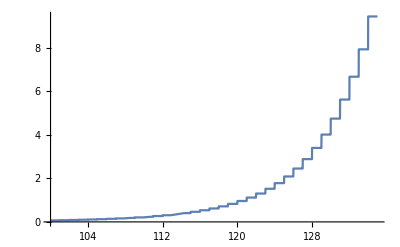

```mathematica
Plot[nicer[b],{b,100,135}]
```

```mathematica
nicer[120]//N
```

0.961014

```mathematica
Sum[b^(b/5+2/3)(Factorial[b]/b^b),{b,34,54,5}]//N
```

0.0261761

```mathematica
Sum[N[b^(b/5+2/3)(Factorial[b]/b^b)],{b,54,100,5}]
```

0.411904

```mathematica
Sum[N[b^(b/5+2/3)(Factorial[b]/b^b)],{b,34,90,5}]
```

0.163179

```mathematica
Sum[N[b^(b/5+2/3)(Factorial[b]/b^b)],{b,90,100,5}]
```

0.365924

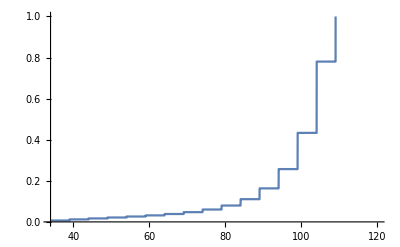

```mathematica
Plot[Sum[N[b^(b/5+2/3)(Factorial[b]/b^b)],{b,34,n,5}],{n,34,120},PlotRange->{0,1}]
```

```mathematica
1
```

```mathematica
b^(b/5+2/3)(Factorial[b]/b^b)/.b->34.
```

0.00683792

```mathematica
99^99/Factorial[99]//N
```

3.96169×10^41